# Generation Helper for βLoop

## Resources

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD-1.1.0/cLTD.m"];
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

```mathematica
FORMPATH="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation/libraries/form/sources/form";(*"<PASTE_HERE_YOUR_FULL_FORM_PATH_HERE_INSTEAD>"*)
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation/libraries/form/sources/form
tFORMpath→tform
WorkingDirectory→./
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

```mathematica
Association[{"a"->1,"b"->2}]
```

<|a→1,b→2|>

```mathematica
PySession=StartExternalSession["Python"];
```

```mathematica
MyExportYAML[content_,file_]:=Block[{},
ResourceFunction["ExportYAML"][PySession,content,file];
ResourceFunction["ExportYAML"][PySession,content,file];
]
```

```mathematica
MyExportYAML[<|"scalar"->5,"alias"->5,"sequence"->{1,2,3},"mapping"->{<|1->"one"|>,<|2->"two"|>,<|3->"three"|>}|>,"/Users/vjhirsch/TMP/test.yaml"]
```

```mathematica
FormatCFFExpr[g_Graph,expr_]:=Module[
{reducedGraph,flipConf,allEsurfs,res,allTerms},
reducedGraph=GraphDifference[g,DirectedGraph[cFFGetExternalEdges[g]]];
allEsurfs={};
allTerms=Table[
flipConf=Association[(Table[#[[iE]]->If[o⟦1⟧[[iE]],-1,1],{iE,Length[#]}]&)@EdgeList[reducedGraph]];
res=FormatCFFTerm[g,flipConf,o⟦2⟧,allEsurfs];
allEsurfs=res⟦1⟧;
<|
"orientation"->(Table[{(#[[iE]]/.{DirectedEdge[_,_,props_]:>props})["id"]-1,If[o⟦1⟧[[iE]],-1,1]},{iE,Length[#]}]&)@EdgeList[reducedGraph],
"factors"->If[ Head[res⟦2⟧]===List,res⟦2⟧,{res⟦2⟧}]
|>
,
{o,expr}
];
<|
"cff_expression"-><|
"terms"->allTerms,
"e_surfaces"->Table[
<|"edge_ids"->Table[eid-1,{eid,allEsurfs⟦esurfID⟧⟦1⟧}],"shift"->allEsurfs⟦esurfID⟧⟦2⟧,"id"->esurfID-1|>
,{esurfID,Length[allEsurfs]}]
|>
|>
]
```

```mathematica
FormatCFFTerm[g_Graph,flipConf_,expr_,allEsurfs_]:=Module[
{currHead,currContent, currCFFterms,nextTerm, oneEsurf,EsurfPos,newallEsurfs,finalRes,res,currDenom,subFactors},
currHead = Head[expr];
currContent=ReplacePart[expr,0->List];
currCFFterms={};
newallEsurfs=allEsurfs;
finalRes=Switch[currHead,
Times,
currDenom=Table[
oneEsurf=Sort[(Esurf/.{Power[x__,-1]:>x}//ReplacePart[#,0->List]&)/.{OSE[y_]:>y}];
oneEsurf={oneEsurf,cFFGenerateEnergyShiftSignatureForEsurf[g,oneEsurf,flipConf]};
EsurfPos=Position[newallEsurfs,oneEsurf];
If[Length[EsurfPos]==1,
oneEsurf=EsurfPos⟦1⟧⟦1⟧-1;
,
AppendTo[newallEsurfs,oneEsurf];
oneEsurf=Length[newallEsurfs]-1;
];
oneEsurf,
{Esurf,Cases[currContent,Power[_,-1]]}];
nextTerm=DeleteCases[currContent,Power[_,-1]];
res=Switch[Length[nextTerm],
1,
FormatCFFTerm[g,flipConf,nextTerm⟦1⟧,newallEsurfs],
0,
{newallEsurfs,{}},
_,
Print["ERROR: Incorrectly formatted cFFTerm"];
{newallEsurfs,nextTerm}
];
newallEsurfs=res[[1]];
subFactors=res⟦2⟧;
<|"denominator"->currDenom,"factors"->subFactors|>,
Plus,
Table[
res=FormatCFFTerm[g,flipConf,e,newallEsurfs];
newallEsurfs=res[[1]];
res[[2]]
,
{e,currContent}],
Power,
If[Or[Length[currContent]!=2,currContent⟦2⟧!=-1],
Print["ERROR: Incorrectly formatted Esurf coef"];
expr
,
oneEsurf=Sort[ReplacePart[currContent⟦1⟧,0->List]/.{OSE[y_]:>y}];
oneEsurf={oneEsurf,cFFGenerateEnergyShiftSignatureForEsurf[g,oneEsurf,flipConf]};
EsurfPos=Position[newallEsurfs,oneEsurf];
If[Length[EsurfPos]==1,
oneEsurf=EsurfPos⟦1⟧⟦1⟧-1;
,
AppendTo[newallEsurfs,oneEsurf];
oneEsurf=Length[newallEsurfs]-1;
];
<|"denominator"->{oneEsurf},"factors"->{}|>
]
,
_,
Print["ERROR: Incorrectly formatted cFFExpression"];
currContent
];
{newallEsurfs,finalRes}
]
```

## loop_induced_TriBoxTri

-Graphics-

--topology = [\
     	(' q1', 0, 1), \
     	(' 2', 1, 3), (' 7', 3, 4), (' 4', 4, 5), \
     	(' 3', 5, 6), (' 6', 6, 7), (' 1', 7, 1), \
     	(' 5', 3, 7), (' 8', 4, 6), \
     	(' q2', 5, 8) ] \
    --masses = [(' 2', 10.), (' 1', 10.), (' 5', 10.), (' 3', 20.), (' 4', 20.), (' 8', 20.), (' 7', 0.), (' 6', 0.),] \
     --lmb = (' 2', ' 4', ' 7') \
      --name = "betaLoop_triangleBoxTriangleBenchmark_scalar" \
       --analytical_result = 0.0 e0 \
         --externals = (' q1',) \
         --numerator = ' 1'

```mathematica
ClearAll[FullLiTriBoxTriSG]
```

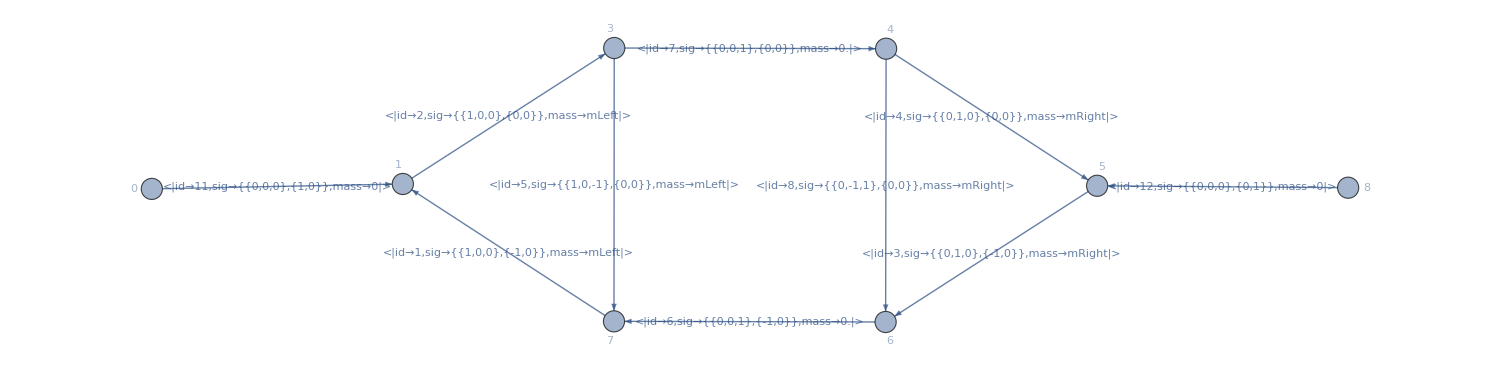

```mathematica
FullLiTriBoxTriSG=DirectedGraph[{
DirectedEdge[1,3,2],DirectedEdge[3,4,7],DirectedEdge[4,5,4],
DirectedEdge[5,6,3],DirectedEdge[6,7,6],DirectedEdge[7,1,1],
DirectedEdge[3,7,5],DirectedEdge[4,6,8],
DirectedEdge[0,1,11],DirectedEdge[8,5,12]
},VertexLabels->Automatic,EdgeLabels->Automatic];
FullLiTriBoxTriSG=DirectedGraph[
AssignSignatures[FullLiTriBoxTriSG,
masses-><|
1->mLeft,2->mLeft,5->mLeft,
6->0.,7->0.,
3->mRight,4->mRight,8->mRight
|>,
lmb->{2,4,7}],
EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->1500,GraphLayout->"SpringEmbedding"]
```

```mathematica
FullLiTriBoxTriSGEdges=Association[Table[e["id"]->e,{e,EdgeList[FullLiTriBoxTriSG]//(#/.DirectedEdge[_,_,props_]:>props)&}]];
```

```mathematica
NumApplication={mLeft->10.,mRight->20.,kvec->{1,3,7},lvec->{9,11,13},mvec->{15,17,19},Qvec->{0,0,0},Q0->100};
```

```mathematica
YAMLSuperGraphRepr=<||>;
```

```mathematica
YAMLSuperGraphRepr["n_loop"]=3;
```

```mathematica
YAMLSuperGraphRepr["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[FullLiTriBoxTriSG,DirectedGraph[cFFGetExternalEdges[FullLiTriBoxTriSG]]]]}]
,
(#["id"])&
]
]
```

{<|mass→10.,signature→{{1,0,0},{-1,0}},id→0,power→1|>,<|mass→10.,signature→{{1,0,0},{0,0}},id→1,power→1|>,<|mass→20.,signature→{{0,1,0},{-1,0}},id→2,power→1|>,<|mass→20.,signature→{{0,1,0},{0,0}},id→3,power→1|>,<|mass→10.,signature→{{1,0,-1},{0,0}},id→4,power→1|>,<|mass→0.,signature→{{0,0,1},{-1,0}},id→5,power→1|>,<|mass→0.,signature→{{0,0,1},{0,0}},id→6,power→1|>,<|mass→20.,signature→{{0,-1,1},{0,0}},id→7,power→1|>}

### Cut (#6, #7)

#### Left triangle of loop_induced_TriBoxTri

```mathematica
TriangleLeftLMBEdges={2};
```

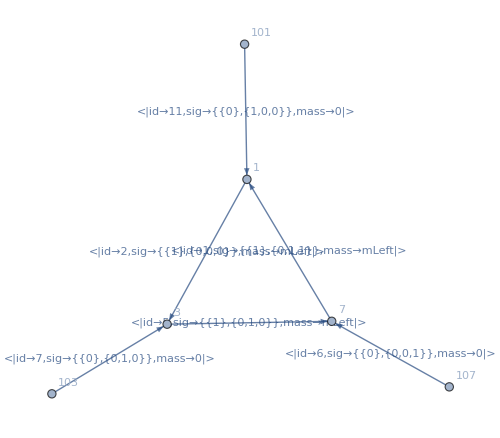

```mathematica
TriangleLeft=DirectedGraph[{
DirectedEdge[1,3,2],DirectedEdge[3,7,5],
DirectedEdge[7,1,1],
DirectedEdge[103,3,7],DirectedEdge[107,7,6],DirectedEdge[101,1,11]
},VertexLabels->Automatic,EdgeLabels->Automatic];
TriangleLeft=DirectedGraph[AssignSignatures[TriangleLeft,masses-><|1->mLeft,2->mLeft,5->mLeft|>,lmb->TriangleLeftLMBEdges],EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

Example evaluation:

```mathematica
TriangleLeftNumerics={mLeft->10.,k1->{1.,2.,3.},p1->{0.,0.,0.},p2->{0.,-3.,-4.},p3->{0.,3.,4.},p1E->10.,p2E->-5.,p3E->-5.};
```

```mathematica
TriangleLeftForCLTDexpr=GeneratecLTDExpression[TriangleLeft];
```

```mathematica
EvalcLTD[TriangleLeftForCLTDexpr,TriangleLeftNumerics]//N//FullForm
```

Complex[0.,-1.99804×10^-6]

```mathematica
TriangleLeftForCFFexpr=CrossFreeFamilyLTD[TriangleLeft,ConvertToNormalisedFormat->True];
```

```mathematica
TriangleLeftForCFFexpr⟦;;1⟧
```

{<|Orientation→<|2→-1,5→-1,1→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{2,1},shift_signature→{0,-1,-1}|>,<|overall_sign→1,OSE→{5,1},shift_signature→{0,0,-1}|>}|>}|>}

```mathematica
EvalcFF[TriangleLeft,TriangleLeftForCFFexpr,TriangleLeftNumerics]//N//FullForm
EvalcFF[TriangleLeft,TriangleLeftForCFFexpr⟦;;1⟧,TriangleLeftNumerics]//N//FullForm
```

Complex[0.,-1.99804×10^-6]

Complex[0.,-1.33424×10^-7]

```mathematica
TriangleLeftcFFexpr=CrossFreeFamilyLTD[TriangleLeft,ConvertToNormalisedFormat->False]
```

{{{True,True,False},1/((OSE[1]+OSE[2]) (OSE[1]+OSE[5]))},{{True,False,True},1/((OSE[1]+OSE[5]) (OSE[2]+OSE[5]))},{{True,False,False},1/((OSE[1]+OSE[2]) (OSE[2]+OSE[5]))},{{False,True,True},1/((OSE[1]+OSE[2]) (OSE[2]+OSE[5]))},{{False,True,False},1/((OSE[1]+OSE[5]) (OSE[2]+OSE[5]))},{{False,False,True},1/((OSE[1]+OSE[2]) (OSE[1]+OSE[5]))}}

```mathematica
YAMLReprTriangleLeft=FormatCFFExpr[TriangleLeft,TriangleLeftcFFexpr];
```

```mathematica
YAMLReprTriangleLeft
```

<|cff_expression→<|terms→{<|orientation→{{1,-1},{4,-1},{0,1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,-1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,1}},factors→{<|denominator→{0,3},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,1}},factors→{<|denominator→{1,5},factors→{}|>}|>,<|orientation→{{1,1},{4,1},{0,-1}},factors→{<|denominator→{4,2},factors→{}|>}|>},e_surfaces→{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}|>|>

```mathematica
YAMLReprTriangleLeft["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[TriangleLeft,DirectedGraph[cFFGetExternalEdges[TriangleLeft]]]]}]
,
(#["id"])&
]
]
```

{<|mass→10.,signature→{{1},{0,1,1}},id→0,power→1|>,<|mass→10.,signature→{{1},{0,0,0}},id→1,power→1|>,<|mass→10.,signature→{{1},{0,1,0}},id→4,power→1|>}

```mathematica
YAMLReprTriangleLeft["lmb_edges"]=Block[{lmbEdges,props},
lmbEdges=Select[EdgeList[TriangleLeft],MemberQ[TriangleLeftLMBEdges,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,lmbEdges}]
,
(Position[TriangleLeftLMBEdges,#["id"]+1]⟦1⟧⟦1⟧)&
]
]
```

{<|mass→10.,signature→{{1},{0,0,0}},id→1,power→1|>}

```mathematica
cFFGetExternalEdges[TriangleLeft]
```

{1011<|id→11,sig→{{0},{1,0,0}},mass→0|>,1033<|id→7,sig→{{0},{0,1,0}},mass→0|>,1077<|id→6,sig→{{0},{0,0,1}},mass→0|>}

```mathematica
YAMLReprTriangleLeft["external_edge_id_and_flip"]={{{-1,1}},{{7-1,-1}},{{6-1,1}}};
YAMLReprTriangleLeft["non_loop_propagators"] = {};
```

```mathematica
YAMLReprTriangleLeft["n_loop"] = 1;
```

```mathematica
YAMLReprTriangleLeft["cff_expression"]["e_surfaces"]
```

{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}

Compute some test externals

```mathematica
testLeftTriBoxTriExtValues=Block[{SGtestpoint,SGtestpointExternals,triBoxTriExt},
SGtestpoint={kvec,lvec,mvec}/.NumApplication;
SGtestpointExternals={Qvec,-Qvec}/.NumApplication;
triBoxTriExt=Table[
FullLiTriBoxTriSGEdges[extID]["sig"]⟦1⟧.SGtestpoint+FullLiTriBoxTriSGEdges[extID]["sig"]⟦2⟧.SGtestpointExternals,
{extID,{11,7,6}}
];
{
Join[{(Q0/.NumApplication)},triBoxTriExt⟦1⟧]*YAMLReprTriangleLeft["external_edge_id_and_flip"]⟦1⟧⟦1⟧⟦2⟧,
Join[
{Sqrt[triBoxTriExt⟦2⟧.triBoxTriExt⟦2⟧+(FullLiTriBoxTriSGEdges[7]["mass"]/.NumApplication)^2]},
triBoxTriExt⟦2⟧
]*YAMLReprTriangleLeft["external_edge_id_and_flip"]⟦2⟧⟦1⟧⟦2⟧,
Join[
(* Watchout for Cutkosoky energy sign here *)
{-Sqrt[triBoxTriExt⟦3⟧.triBoxTriExt⟦3⟧+(FullLiTriBoxTriSGEdges[6]["mass"]/.NumApplication)^2]},
triBoxTriExt⟦3⟧
]*YAMLReprTriangleLeft["external_edge_id_and_flip"]⟦3⟧⟦1⟧⟦2⟧
}
]
```

{{100,0,0,0},{-29.5804,-15,-17,-19},{-29.5804,15,17,19}}

As expected since the is the triangle to the left of the Cutkosky cut with all momenta incoming, then the Qvec as positive energy but the other two from the Cutkosky cut that are also incoming into the triangle have negative energy.
Now when evaluating the energy shifts of the E-surface, defined as, Sqrt(...)+Sqrt(...)+*PLUS* Eshift, we must retain only those with positive Eshift as existing and threshold to regularise. Of course. for the real alphaLoop, all of this must be done dynamically at run time.

Now, we can specify as threshold only those with a negative energy shift

```mathematica
Table[{es,es["shift"].Table[ext⟦1⟧,{ext,testLeftTriBoxTriExtValues}]},{es,YAMLReprTriangleLeft["cff_expression"]["e_surfaces"]}]
```

{{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,59.1608},{<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,29.5804},{<|edge_ids→{0,4},shift→{0,0,1},id→2|>,-29.5804},{<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,29.5804},{<|edge_ids→{0,1},shift→{0,1,1},id→4|>,-59.1608},{<|edge_ids→{1,4},shift→{0,1,0},id→5|>,-29.5804}}

```mathematica
(*
YAMLReprTriangleLeft["thresholds"] = Table[es["id"],{es,Select[YAMLReprTriangleLeft["cff_expression"]["e_surfaces"],((#["shift"].Table[ext⟦1⟧,{ext,testLeftTriBoxTriExtValues}])<0)&]}]
*)
```

```mathematica
YAMLReprTriangleLeft
```

<|cff_expression→<|terms→{<|orientation→{{1,-1},{4,-1},{0,1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,-1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,1}},factors→{<|denominator→{0,3},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,1}},factors→{<|denominator→{1,5},factors→{}|>}|>,<|orientation→{{1,1},{4,1},{0,-1}},factors→{<|denominator→{4,2},factors→{}|>}|>},e_surfaces→{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}|>,edges→{<|mass→10.,signature→{{1},{0,1,1}},id→0,power→1|>,<|mass→10.,signature→{{1},{0,0,0}},id→1,power→1|>,<|mass→10.,signature→{{1},{0,1,0}},id→4,power→1|>},lmb_edges→{<|mass→10.,signature→{{1},{0,0,0}},id→1,power→1|>},external_edge_id_and_flip→{{{-1,1}},{{6,-1}},{{5,1}}},non_loop_propagators→{},n_loop→1|>

```mathematica
(*MyExportYAML[YAMLReprTriangleLeft,NotebookDirectory[]<>"../data/loop_induced_TriBoxTri_left_triangle.yaml"]*)
```

#### Right triangle of loop_induced_TriBoxTri

```mathematica
TriangleRightLMBEdges={4};
```

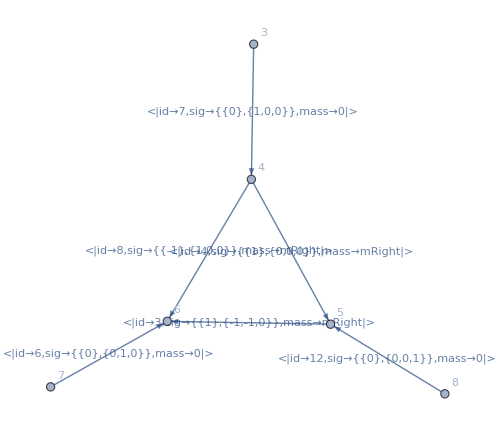

```mathematica
TriangleRight=DirectedGraph[{
DirectedEdge[4,5,4],DirectedEdge[4,6,8],DirectedEdge[5,6,3],
DirectedEdge[3,4,7],DirectedEdge[7,6,6],DirectedEdge[8,5,12]
},VertexLabels->Automatic,EdgeLabels->Automatic];
TriangleRight=DirectedGraph[AssignSignatures[TriangleRight,masses-><|4->mRight,8->mRight,3->mRight|>,lmb->TriangleRightLMBEdges],EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

Example evaluation:

```mathematica
TriangleRightNumerics={mRight->20.,k1->{4.,5.,6.},p3->{0.,0.,0.},p1->{0.,3.,4.},p2->{0.,-3.,-4.},p3E->-10.,p1E->5.,p2E->5.};
```

```mathematica
TriangleRightForCLTDexpr=GeneratecLTDExpression[TriangleRight];
```

```mathematica
EvalcLTD[TriangleRightForCLTDexpr,TriangleRightNumerics]
```

0.-4.4522×10^-8 ⅈ

```mathematica
TriangleRightForCFFexpr=CrossFreeFamilyLTD[TriangleRight,ConvertToNormalisedFormat->True];
```

```mathematica
TriangleRightForCFFexpr⟦;;1⟧
```

{<|Orientation→<|4→-1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>}

```mathematica
TriangleRightForCFFexpr
```

{<|Orientation→<|4→-1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>,<|Orientation→<|4→-1,8→-1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{4,3},shift_signature→{1,1,0}|>}|>}|>,<|Orientation→<|4→-1,8→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{8,3},shift_signature→{0,1,0}|>,<|overall_sign→1,OSE→{4,3},shift_signature→{1,1,0}|>}|>}|>,<|Orientation→<|4→1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,3},shift_signature→{-1,-1,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>,<|Orientation→<|4→1,8→1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,3},shift_signature→{-1,-1,0}|>,<|overall_sign→1,OSE→{4,8},shift_signature→{-1,0,0}|>}|>}|>,<|Orientation→<|4→1,8→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{8,3},shift_signature→{0,1,0}|>,<|overall_sign→1,OSE→{4,8},shift_signature→{-1,0,0}|>}|>}|>}

```mathematica
EvalcFF[TriangleRight,TriangleRightForCFFexpr,TriangleRightNumerics]//N//FullForm
Table[EvalcFF[TriangleRight,{cf},TriangleRightNumerics],{cf,TriangleRightForCFFexpr}]//N//FullForm
```

Complex[0.,-4.4522×10^-8]

List[Complex[0.,-7.16808×10^-9],Complex[0.,-4.99831×10^-9],Complex[0.,-4.99831×10^-9],Complex[0.,-1.00946×10^-8],Complex[0.,-1.00946×10^-8],Complex[0.,-7.16808×10^-9]]

[7.16807842383469428413203009814776018 e - 09, 4.99830992408741204854054414056956505 e - 09, 7.16807842383469428413203009814776018 e - 09, 1.00946170067175641017834306368175397 e - 08, 
7.16807842383469428413203009814776018 e - 09, 7.03898888672392565940294860153405232 e - 09]

```mathematica
EvalcFF[TriangleRight,{TriangleRightForCFFexpr⟦3⟧},TriangleRightNumerics]
```

0.-4.99831×10^-9 ⅈ

```mathematica
YAMLReprTriangleRight
```

<|cff_expression→<|terms→{<|orientation→{{3,-1},{7,-1},{2,-1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,-1},{2,1}},factors→{<|denominator→{2,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,1},{2,1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{3,1},{7,-1},{2,-1}},factors→{<|denominator→{4,0},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,1}},factors→{<|denominator→{3,5},factors→{}|>}|>},e_surfaces→{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}|>,edges→{<|mass→20.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→20.,signature→{{-1},{1,0,0}},id→7,power→1|>},lmb_edges→{<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>},external_edge_id_and_flip→{{{6,1}},{{5,-1}},{{-2,1}}},non_loop_propagators→{},n_loop→1|>

```mathematica
TriangleRightcFFexpr=CrossFreeFamilyLTD[TriangleRight,ConvertToNormalisedFormat->False]
```

{{{True,True,True},1/((OSE[3]+OSE[8]) (OSE[4]+OSE[8]))},{{True,True,False},1/((OSE[3]+OSE[4]) (OSE[4]+OSE[8]))},{{True,False,False},1/((OSE[3]+OSE[4]) (OSE[3]+OSE[8]))},{{False,True,True},1/((OSE[3]+OSE[4]) (OSE[3]+OSE[8]))},{{False,False,True},1/((OSE[3]+OSE[4]) (OSE[4]+OSE[8]))},{{False,False,False},1/((OSE[3]+OSE[8]) (OSE[4]+OSE[8]))}}

```mathematica
YAMLReprTriangleRight=FormatCFFExpr[TriangleRight,TriangleRightcFFexpr];
```

```mathematica
YAMLReprTriangleRight["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[TriangleRight,DirectedGraph[cFFGetExternalEdges[TriangleRight]]]]}]
,
(#["id"])&
]
]
```

{<|mass→20.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→20.,signature→{{-1},{1,0,0}},id→7,power→1|>}

```mathematica
YAMLReprTriangleRight["lmb_edges"]=Block[{lmbEdges,props},
lmbEdges=Select[EdgeList[TriangleRight],MemberQ[TriangleRightLMBEdges,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,lmbEdges}]
,
(Position[TriangleRightLMBEdges,#["id"]+1]⟦1⟧⟦1⟧)&
]
]
```

{<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>}

```mathematica
cFFGetExternalEdges[TriangleRight]
```

{34<|id→7,sig→{{0},{1,0,0}},mass→0|>,76<|id→6,sig→{{0},{0,1,0}},mass→0|>,85<|id→12,sig→{{0},{0,0,1}},mass→0|>}

```mathematica
YAMLReprTriangleRight["external_edge_id_and_flip"]={{{7-1,1}},{{6-1,-1}},{{-2,-1}}};
YAMLReprTriangleRight["non_loop_propagators"] = {};
```

```mathematica
YAMLReprTriangleRight["n_loop"] = 1;
```

```mathematica
YAMLReprTriangleRight["cff_expression"]["e_surfaces"]
```

{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}

Compute some test externals

```mathematica
testRightTriBoxTriExtValues=Block[{SGtestpoint,SGtestpointExternals,triBoxTriExt},
SGtestpoint={kvec,lvec,mvec}/.NumApplication;
SGtestpointExternals={Qvec,-Qvec}/.NumApplication;
triBoxTriExt=Table[
FullLiTriBoxTriSGEdges[extID]["sig"]⟦1⟧.SGtestpoint+FullLiTriBoxTriSGEdges[extID]["sig"]⟦2⟧.SGtestpointExternals,
{extID,{7,6,12}}
];
{
Join[
{Sqrt[triBoxTriExt⟦1⟧.triBoxTriExt⟦1⟧+(FullLiTriBoxTriSGEdges[7]["mass"]/.NumApplication)^2]},
triBoxTriExt⟦1⟧
]*YAMLReprTriangleRight["external_edge_id_and_flip"]⟦1⟧⟦1⟧⟦2⟧,
Join[
(* Watchout for Cutkosoky energy sign here *)
{-Sqrt[triBoxTriExt⟦2⟧.triBoxTriExt⟦2⟧+(FullLiTriBoxTriSGEdges[6]["mass"]/.NumApplication)^2]},
triBoxTriExt⟦2⟧
]*YAMLReprTriangleRight["external_edge_id_and_flip"]⟦2⟧⟦1⟧⟦2⟧,
(* Sign flip necessary here too *)
Join[{(-Q0/.NumApplication)},triBoxTriExt⟦1⟧]*YAMLReprTriangleRight["external_edge_id_and_flip"]⟦3⟧⟦1⟧⟦2⟧
}
]
```

{{29.5804,15,17,19},{29.5804,-15,-17,-19},{100,-15,-17,-19}}

As expected since the is the triangle to the right of the Cutkosky cut with all momenta incoming, then the Qvec as positive energy but the other two from the Cutkosky cut that are also incoming into the triangle have negative energy.
Now when evaluating the energy shifts of the E-surface, defined as, Sqrt(...)+Sqrt(...)+*PLUS* Eshift, we must retain only those with positive Eshift as existing and threshold to regularise. Of course. for the real alphaLoop, all of this must be done dynamically at run time.

Now, we can specify as threshold only those with a negative energy shift

```mathematica
Table[{es,es["shift"].Table[ext⟦1⟧,{ext,testRightTriBoxTriExtValues}]},{es,YAMLReprTriangleRight["cff_expression"]["e_surfaces"]}]
```

{{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,-29.5804},{<|edge_ids→{3,7},shift→{1,0,0},id→1|>,29.5804},{<|edge_ids→{2,3},shift→{1,1,0},id→2|>,59.1608},{<|edge_ids→{2,7},shift→{0,1,0},id→3|>,29.5804},{<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,-59.1608},{<|edge_ids→{3,7},shift→{-1,0,0},id→5|>,-29.5804}}

```mathematica
(*
YAMLReprTriangleRight["thresholds"] = Table[es["id"],{es,Select[YAMLReprTriangleRight["cff_expression"]["e_surfaces"],((#["shift"].Table[ext⟦1⟧,{ext,testRightTriBoxTriExtValues}])<0)&]}]
*)
```

```mathematica
TriangleRightcFFexpr
```

{{{True,True,True},1/((OSE[3]+OSE[8]) (OSE[4]+OSE[8]))},{{True,True,False},1/((OSE[3]+OSE[4]) (OSE[4]+OSE[8]))},{{True,False,False},1/((OSE[3]+OSE[4]) (OSE[3]+OSE[8]))},{{False,True,True},1/((OSE[3]+OSE[4]) (OSE[3]+OSE[8]))},{{False,False,True},1/((OSE[3]+OSE[4]) (OSE[4]+OSE[8]))},{{False,False,False},1/((OSE[3]+OSE[8]) (OSE[4]+OSE[8]))}}

```mathematica
CrossFreeFamilyLTD[TriangleRight,ConvertToNormalisedFormat->True]
```

{<|Orientation→<|4→-1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>,<|Orientation→<|4→-1,8→-1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{4,3},shift_signature→{1,1,0}|>}|>}|>,<|Orientation→<|4→-1,8→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{8,3},shift_signature→{0,1,0}|>,<|overall_sign→1,OSE→{4,3},shift_signature→{1,1,0}|>}|>}|>,<|Orientation→<|4→1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,3},shift_signature→{-1,-1,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>,<|Orientation→<|4→1,8→1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,3},shift_signature→{-1,-1,0}|>,<|overall_sign→1,OSE→{4,8},shift_signature→{-1,0,0}|>}|>}|>,<|Orientation→<|4→1,8→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{8,3},shift_signature→{0,1,0}|>,<|overall_sign→1,OSE→{4,8},shift_signature→{-1,0,0}|>}|>}|>}

```mathematica
YAMLReprTriangleRight
```

<|cff_expression→<|terms→{<|orientation→{{3,-1},{7,-1},{2,-1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,-1},{2,1}},factors→{<|denominator→{2,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,1},{2,1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{3,1},{7,-1},{2,-1}},factors→{<|denominator→{4,0},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,1}},factors→{<|denominator→{3,5},factors→{}|>}|>},e_surfaces→{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}|>,edges→{<|mass→20.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→20.,signature→{{-1},{1,0,0}},id→7,power→1|>},lmb_edges→{<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>},external_edge_id_and_flip→{{{6,1}},{{5,-1}},{{-2,-1}}},non_loop_propagators→{},n_loop→1|>

### Cut definitions

```mathematica
YAMLSuperGraphRepr["cuts"]={};
```

```mathematica
Cut67= <|
"cut_edge_ids_and_flip"->{{6-1,-1},{7-1,1}},
"left_amplitude"->YAMLReprTriangleLeft,
"right_amplitude"->YAMLReprTriangleRight
|>
```

<|cut_edge_ids_and_flip→{{5,-1},{6,1}},left_amplitude→<|cff_expression→<|terms→{<|orientation→{{1,-1},{4,-1},{0,1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,-1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,1}},factors→{<|denominator→{0,3},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,1}},factors→{<|denominator→{1,5},factors→{}|>}|>,<|orientation→{{1,1},{4,1},{0,-1}},factors→{<|denominator→{4,2},factors→{}|>}|>},e_surfaces→{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}|>,edges→{<|mass→10.,signature→{{1},{0,1,1}},id→0,power→1|>,<|mass→10.,signature→{{1},{0,0,0}},id→1,power→1|>,<|mass→10.,signature→{{1},{0,1,0}},id→4,power→1|>},lmb_edges→{<|mass→10.,signature→{{1},{0,0,0}},id→1,power→1|>},external_edge_id_and_flip→{{{-1,1}},{{6,-1}},{{5,1}}},non_loop_propagators→{},n_loop→1|>,right_amplitude→<|cff_expression→<|terms→{<|orientation→{{3,-1},{7,-1},{2,-1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,-1},{2,1}},factors→{<|denominator→{2,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,1},{2,1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{3,1},{7,-1},{2,-1}},factors→{<|denominator→{4,0},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,1}},factors→{<|denominator→{3,5},factors→{}|>}|>},e_surfaces→{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}|>,edges→{<|mass→20.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→20.,signature→{{-1},{1,0,0}},id→7,power→1|>},lmb_edges→{<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>},external_edge_id_and_flip→{{{6,1}},{{5,-1}},{{-2,-1}}},non_loop_propagators→{},n_loop→1|>|>

```mathematica
AppendTo[YAMLSuperGraphRepr["cuts"],Cut67];
```

### Export Supergraph

```mathematica
YAMLSuperGraphRepr
```

<|n_loop→3,edges→{<|mass→10.,signature→{{1,0,0},{-1,0}},id→0,power→1|>,<|mass→10.,signature→{{1,0,0},{0,0}},id→1,power→1|>,<|mass→20.,signature→{{0,1,0},{-1,0}},id→2,power→1|>,<|mass→20.,signature→{{0,1,0},{0,0}},id→3,power→1|>,<|mass→10.,signature→{{1,0,-1},{0,0}},id→4,power→1|>,<|mass→0.,signature→{{0,0,1},{-1,0}},id→5,power→1|>,<|mass→0.,signature→{{0,0,1},{0,0}},id→6,power→1|>,<|mass→20.,signature→{{0,-1,1},{0,0}},id→7,power→1|>},cuts→{<|cut_edge_ids_and_flip→{{5,-1},{6,1}},left_amplitude→<|cff_expression→<|terms→{<|orientation→{{1,-1},{4,-1},{0,1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,-1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,1}},factors→{<|denominator→{0,3},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,1}},factors→{<|denominator→{1,5},factors→{}|>}|>,<|orientation→{{1,1},{4,1},{0,-1}},factors→{<|denominator→{4,2},factors→{}|>}|>},e_surfaces→{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}|>,edges→{<|mass→10.,signature→{{1},{0,1,1}},id→0,power→1|>,<|mass→10.,signature→{{1},{0,0,0}},id→1,power→1|>,<|mass→10.,signature→{{1},{0,1,0}},id→4,power→1|>},lmb_edges→{<|mass→10.,signature→{{1},{0,0,0}},id→1,power→1|>},external_edge_id_and_flip→{{{-1,1}},{{6,-1}},{{5,1}}},non_loop_propagators→{},n_loop→1|>,right_amplitude→<|cff_expression→<|terms→{<|orientation→{{3,-1},{7,-1},{2,-1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,-1},{2,1}},factors→{<|denominator→{2,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,1},{2,1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{3,1},{7,-1},{2,-1}},factors→{<|denominator→{4,0},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,1}},factors→{<|denominator→{3,5},factors→{}|>}|>},e_surfaces→{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}|>,edges→{<|mass→20.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→20.,signature→{{-1},{1,0,0}},id→7,power→1|>},lmb_edges→{<|mass→20.,signature→{{1},{0,0,0}},id→3,power→1|>},external_edge_id_and_flip→{{{6,1}},{{5,-1}},{{-2,-1}}},non_loop_propagators→{},n_loop→1|>|>}|>

```mathematica
YAMLSuperGraphRepr["cuts"]⟦1⟧["left_amplitude"]["cff_expression"]["terms"]⟦1⟧["factors"]⟦1⟧
```

<|denominator→{0,1},factors→{}|>

```mathematica
MyExportYAML[YAMLSuperGraphRepr,NotebookDirectory[]<>"../data/loop_induced_TriBoxTri.yaml"]
```

## LUTriBoxTri

-Graphics-
import model aL_sm-no_widths
set_alphaLoop_option perturbative_orders {‘QCD’:4}
set_alphaLoop_option n_rust_inputs_to_generate -1
set_alphaLoop_option include_self_energies_from_squared_amplitudes True
set_alphaLoop_option differentiate_particle_from_antiparticle_in_graph_isomorphism False
set_alphaLoop_option consider_vertex_id_in_graph_isomorphism False
set_alphaLoop_option consider_edge_orientation_in_graph_isomorphism False
set_alphaLoop_option FORM_processing_output_format c
set_alphaLoop_option FORM_compile_arg all
set_alphaLoop_option apply_graph_isomorphisms True
set_alphaLoop_option qgraf_template_model no_s
set_FORM_option number_of_lmbs None

set_alphaLoop_option FORM_compile_cores 8
set_FORM_option cores 8

set_alphaLoop_option qgraf_model SM
set_FORM_option generate_integrated_UV_CTs True
set_FORM_option generate_renormalisation_graphs False
set_alphaLoop_option FORM_compile_optimization 1
set_alphaLoop_option FORM_integrand_type both
set_FORM_option generate_arb_prec_output True
set_FORM_option on_shell_renormalisation True

set_alphaLoop_option SG_name_list [“SG_QG3”,]
set_alphaLoop_option checkpoint_lvl 1
set_FORM_option reference_lmb {“SG_QG3”:[“pq2”,”pq4”,”pq7”],}
qgraf_define j = d d~ g gh gh~
qgraf_generate a > d d~ / u s c b QCD^2==2 QED^2==1 [QCD QCD]
!rm -rf betaLoop_triangleBoxTriangleBenchmark
output qgraf betaLoop_triangleBoxTriangleBenchmark

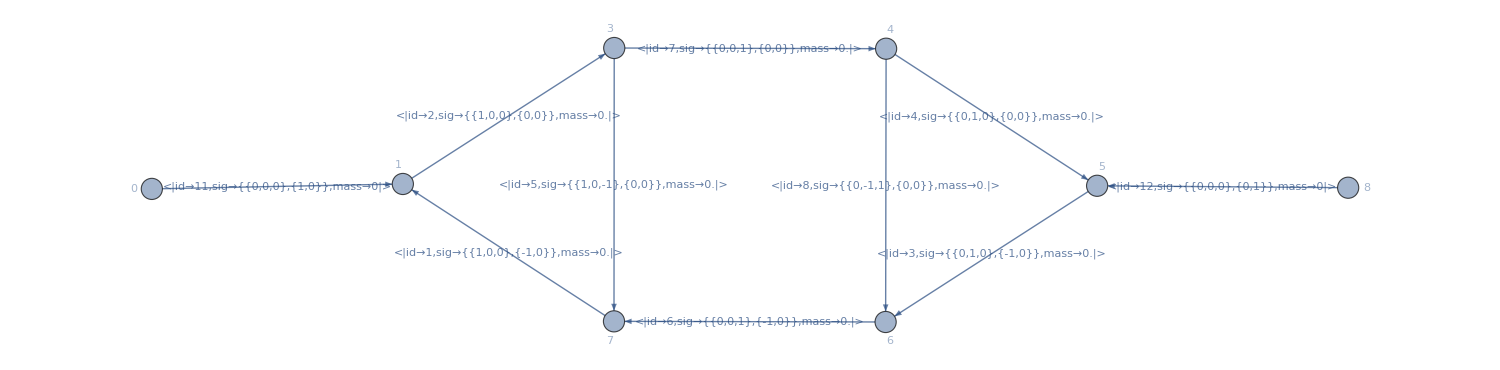

```mathematica
LUFullLiTriBoxTriSG=DirectedGraph[{
DirectedEdge[1,3,2],DirectedEdge[3,4,7],DirectedEdge[4,5,4],
DirectedEdge[5,6,3],DirectedEdge[6,7,6],DirectedEdge[7,1,1],
DirectedEdge[3,7,5],DirectedEdge[4,6,8],
DirectedEdge[0,1,11],DirectedEdge[8,5,12]
},VertexLabels->Automatic,EdgeLabels->Automatic];
LUFullLiTriBoxTriSG=DirectedGraph[
AssignSignatures[LUFullLiTriBoxTriSG,
masses-><|
1->0.,2->0.,5->0.,
6->0.,7->0.,
3->0.,4->0.,8->0.
|>,
lmb->{2,4,7}],
EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->1500,GraphLayout->"SpringEmbedding"]
```

```mathematica
LUFullLiTriBoxTriSGEdges=Association[Table[e["id"]->e,{e,EdgeList[LUFullLiTriBoxTriSG]//(#/.DirectedEdge[_,_,props_]:>props)&}]];
```

```mathematica
LUNumApplication={kvec->{1,3,7},lvec->{9,11,13},mvec->{15,17,19},Qvec->{0,0,0},Q0->100};
```

```mathematica
YAMLSuperGraphRepr=<||>;
```

```mathematica
YAMLSuperGraphRepr["n_loop"]=3;
```

```mathematica
YAMLSuperGraphRepr["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.LUNumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[LUFullLiTriBoxTriSG,DirectedGraph[cFFGetExternalEdges[LUFullLiTriBoxTriSG]]]]}]
,
(#["id"])&
]
]
```

{<|mass→0.,signature→{{1,0,0},{-1,0}},id→0,power→1|>,<|mass→0.,signature→{{1,0,0},{0,0}},id→1,power→1|>,<|mass→0.,signature→{{0,1,0},{-1,0}},id→2,power→1|>,<|mass→0.,signature→{{0,1,0},{0,0}},id→3,power→1|>,<|mass→0.,signature→{{1,0,-1},{0,0}},id→4,power→1|>,<|mass→0.,signature→{{0,0,1},{-1,0}},id→5,power→1|>,<|mass→0.,signature→{{0,0,1},{0,0}},id→6,power→1|>,<|mass→0.,signature→{{0,-1,1},{0,0}},id→7,power→1|>}

```mathematica
YAMLSuperGraphRepr["cuts"]={};
```

### Cut (#1, #2)

```mathematica
Cut12RightLMBEdges={4,7};
```

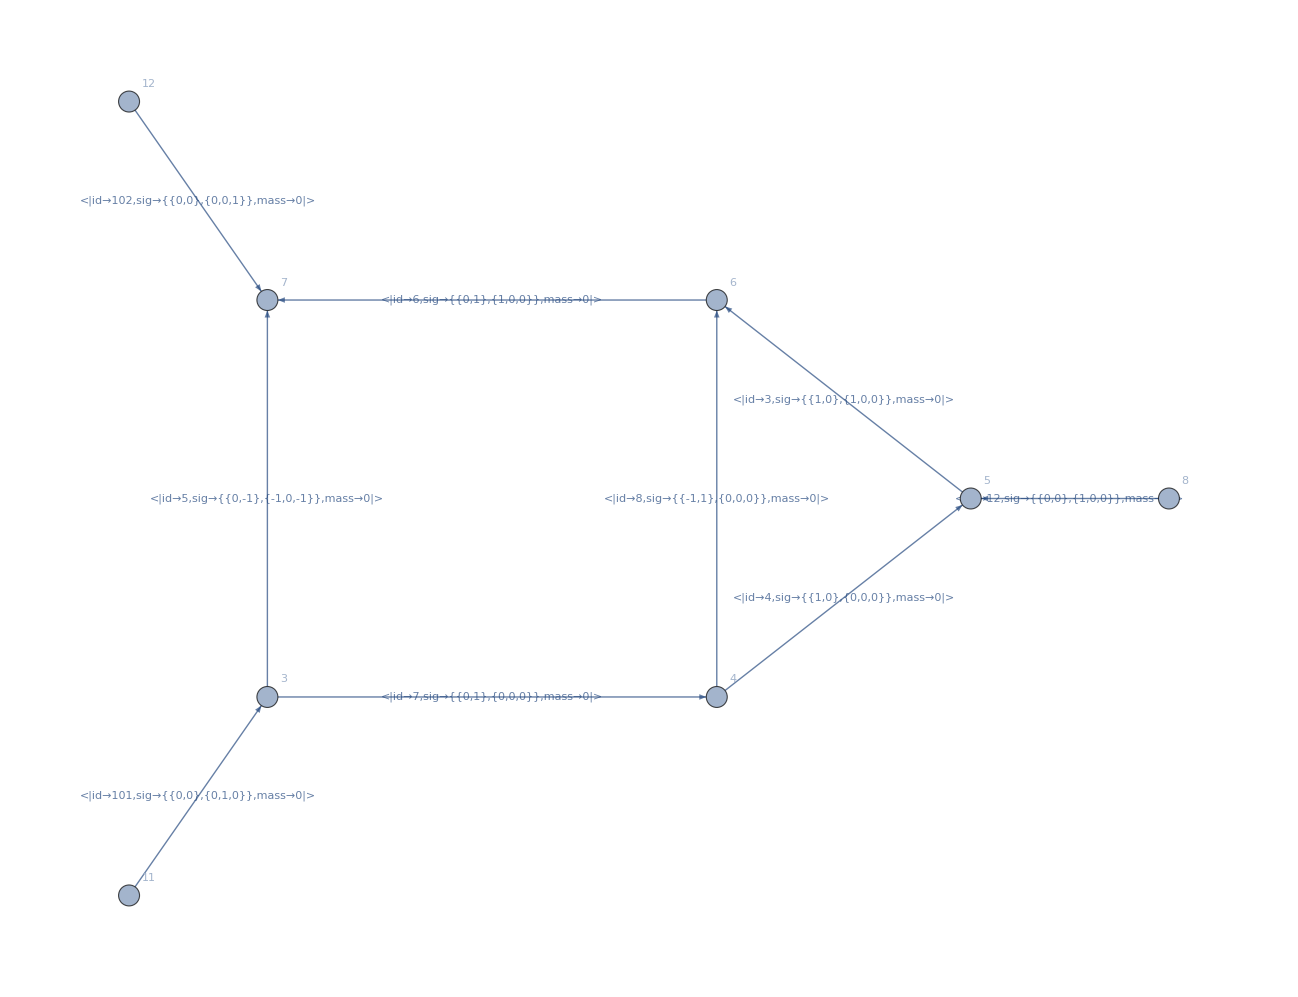

```mathematica
Cut12Right=DirectedGraph[{
DirectedEdge[3,4,7],DirectedEdge[4,5,4],
DirectedEdge[5,6,3],DirectedEdge[6,7,6],
DirectedEdge[3,7,5],DirectedEdge[4,6,8],
DirectedEdge[8,5,12],
DirectedEdge[11,3,101],DirectedEdge[12,7,102]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Cut12Right=DirectedGraph[AssignSignatures[Cut12Right,masses-><||>,lmb->Cut12RightLMBEdges],EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
Cut12RightcFFexpr=CrossFreeFamilyLTD[Cut12Right,ConvertToNormalisedFormat->False];
```

```mathematica
YAMLCut12Right=FormatCFFExpr[Cut12Right,Cut12RightcFFexpr];
```

```mathematica
YAMLCut12Right;
```

```mathematica
YAMLCut12Right["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"],
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[Cut12Right,DirectedGraph[cFFGetExternalEdges[Cut12Right]]]]}]
,
(#["id"])&
]
]
```

{<|mass→0,signature→{{1,0},{1,0,0}},id→2,power→1|>,<|mass→0,signature→{{1,0},{0,0,0}},id→3,power→1|>,<|mass→0,signature→{{0,-1},{-1,0,-1}},id→4,power→1|>,<|mass→0,signature→{{0,1},{1,0,0}},id→5,power→1|>,<|mass→0,signature→{{0,1},{0,0,0}},id→6,power→1|>,<|mass→0,signature→{{-1,1},{0,0,0}},id→7,power→1|>}

```mathematica
YAMLCut12Right["lmb_edges"]=Block[{lmbEdges,props},
lmbEdges=Select[EdgeList[Cut12Right],MemberQ[Cut12RightLMBEdges,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"],
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,lmbEdges}]
,
(Position[Cut12RightLMBEdges,#["id"]+1]⟦1⟧⟦1⟧)&
]
]
```

{<|mass→0,signature→{{1,0},{0,0,0}},id→3,power→1|>,<|mass→0,signature→{{0,1},{0,0,0}},id→6,power→1|>}

```mathematica
cFFGetExternalEdges[Cut12Right]
```

{85<|id→12,sig→{{0,0},{1,0,0}},mass→0|>,113<|id→101,sig→{{0,0},{0,1,0}},mass→0|>,127<|id→102,sig→{{0,0},{0,0,1}},mass→0|>}

```mathematica
(* Reconstruct externals from orientated sums of Cutkosky cut oriented onshell momenta *)
(* Negative momenta refer to overall SG externals *)
YAMLCut12Right["external_edge_id_and_flip"]={{{-2,-1}},{{2-1,1}},{{1-1,-1}}};
(* Specify propagators outside of loop using oriented sum of oriented Cutkosky cut onshell momenta *)
YAMLCut12Right["non_loop_propagators"] = {};
```

```mathematica
YAMLCut12Right["n_loop"] = 2;
```

```mathematica
YAMLCut12Right["cff_expression"]["e_surfaces"]
```

{<|edge_ids→{4,5},shift→{0,0,-1},id→0|>,<|edge_ids→{4,6},shift→{-1,0,-1},id→1|>,<|edge_ids→{2,4,7},shift→{0,0,-1},id→2|>,<|edge_ids→{3,4,7},shift→{-1,0,-1},id→3|>,<|edge_ids→{5,6},shift→{-1,0,0},id→4|>,<|edge_ids→{2,5,7},shift→{0,0,0},id→5|>,<|edge_ids→{3,5,7},shift→{-1,0,0},id→6|>,<|edge_ids→{2,3},shift→{-1,0,0},id→7|>,<|edge_ids→{2,6,7},shift→{-1,0,0},id→8|>,<|edge_ids→{2,3},shift→{1,0,0},id→9|>,<|edge_ids→{3,5,7},shift→{1,0,0},id→10|>,<|edge_ids→{3,6,7},shift→{0,0,0},id→11|>,<|edge_ids→{4,5},shift→{0,0,1},id→12|>,<|edge_ids→{2,4,7},shift→{0,0,1},id→13|>,<|edge_ids→{3,4,7},shift→{1,0,1},id→14|>,<|edge_ids→{2,6,7},shift→{1,0,0},id→15|>,<|edge_ids→{5,6},shift→{1,0,0},id→16|>,<|edge_ids→{4,6},shift→{1,0,1},id→17|>}

```mathematica
YAMLCut12Right;
```

```mathematica
YAMLCut12Left=<|
"edges"->{},
"lmb_edges"->{},
"external_edge_id_and_flip"->{},
"n_loop"->0,
"non_loop_propagators"->{},
"cff_expression"-><|
"e_surfaces"->{},
"terms"->{
<|
"orientation"->{},
"factors"->{
<|
"denominator"->{},
"factors"->{}
|>
}
|>
}
|>
|>
```

<|edges→{},lmb_edges→{},external_edge_id_and_flip→{},n_loop→0,non_loop_propagators→{},cff_expression→<|e_surfaces→{},terms→{<|orientation→{},factors→{<|denominator→{},factors→{}|>}|>}|>|>

```mathematica
Cut12= <|
"cut_edge_ids_and_flip"->{{1-1,-1},{2-1,1}},
"left_amplitude"->YAMLCut12Left,
"right_amplitude"->YAMLCut12Right
|>;
AppendTo[YAMLSuperGraphRepr["cuts"],Cut12];
```

### Cut (#3, #4)

```mathematica
Cut34LeftLMBEdges={2,7};
```

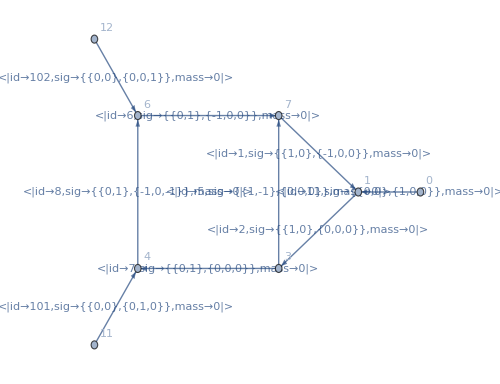

```mathematica
Cut34Left=DirectedGraph[{
DirectedEdge[1,3,2],DirectedEdge[3,4,7],
DirectedEdge[6,7,6],DirectedEdge[7,1,1],
DirectedEdge[3,7,5],DirectedEdge[4,6,8],
DirectedEdge[0,1,11],
DirectedEdge[11,4,101],DirectedEdge[12,6,102]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Cut34Left=DirectedGraph[AssignSignatures[Cut34Left,masses-><||>,lmb->Cut34LeftLMBEdges],EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
Cut34LeftcFFexpr=CrossFreeFamilyLTD[Cut34Left,ConvertToNormalisedFormat->False];
```

```mathematica
YAMLCut34Left=FormatCFFExpr[Cut34Left,Cut34LeftcFFexpr];
```

```mathematica
YAMLCut34Left;
```

```mathematica
YAMLCut34Left["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"],
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[Cut34Left,DirectedGraph[cFFGetExternalEdges[Cut34Left]]]]}]
,
(#["id"])&
]
]
```

{<|mass→0,signature→{{1,0},{-1,0,0}},id→0,power→1|>,<|mass→0,signature→{{1,0},{0,0,0}},id→1,power→1|>,<|mass→0,signature→{{1,-1},{0,0,0}},id→4,power→1|>,<|mass→0,signature→{{0,1},{-1,0,0}},id→5,power→1|>,<|mass→0,signature→{{0,1},{0,0,0}},id→6,power→1|>,<|mass→0,signature→{{0,1},{-1,0,-1}},id→7,power→1|>}

```mathematica
YAMLCut34Left["lmb_edges"]=Block[{lmbEdges,props},
lmbEdges=Select[EdgeList[Cut34Left],MemberQ[Cut34LeftLMBEdges,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"],
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,lmbEdges}]
,
(Position[Cut34LeftLMBEdges,#["id"]+1]⟦1⟧⟦1⟧)&
]
]
```

{<|mass→0,signature→{{1,0},{0,0,0}},id→1,power→1|>,<|mass→0,signature→{{0,1},{0,0,0}},id→6,power→1|>}

```mathematica
cFFGetExternalEdges[Cut34Left]
```

{01<|id→11,sig→{{0,0},{1,0,0}},mass→0|>,114<|id→101,sig→{{0,0},{0,1,0}},mass→0|>,126<|id→102,sig→{{0,0},{0,0,1}},mass→0|>}

```mathematica
(* Reconstruct externals from orientated sums of Cutkosky cut oriented onshell momenta *)
(* Negative momenta refer to overall SG externals *)
YAMLCut34Left["external_edge_id_and_flip"]={{{-1,1}},{{4-1,-1}},{{3-1,1}}};
(* Specify propagators outside of loop using oriented sum of oriented Cutkosky cut onshell momenta *)
YAMLCut34Left["non_loop_propagators"] = {};
```

```mathematica
YAMLCut34Left["n_loop"] = 2;
```

```mathematica
YAMLCut34Left["cff_expression"]["e_surfaces"]
```

{<|edge_ids→{0,1},shift→{1,0,0},id→0|>,<|edge_ids→{0,4,5},shift→{0,0,0},id→1|>,<|edge_ids→{0,4,6},shift→{1,0,0},id→2|>,<|edge_ids→{0,4,7},shift→{0,0,-1},id→3|>,<|edge_ids→{5,6},shift→{1,0,0},id→4|>,<|edge_ids→{5,7},shift→{0,0,-1},id→5|>,<|edge_ids→{5,7},shift→{0,0,1},id→6|>,<|edge_ids→{6,7},shift→{1,0,1},id→7|>,<|edge_ids→{1,4,5},shift→{1,0,0},id→8|>,<|edge_ids→{0,4,7},shift→{0,0,1},id→9|>,<|edge_ids→{1,4,7},shift→{1,0,1},id→10|>,<|edge_ids→{6,7},shift→{-1,0,-1},id→11|>,<|edge_ids→{5,6},shift→{-1,0,0},id→12|>,<|edge_ids→{0,4,6},shift→{-1,0,0},id→13|>,<|edge_ids→{1,4,6},shift→{0,0,0},id→14|>,<|edge_ids→{0,1},shift→{-1,0,0},id→15|>,<|edge_ids→{1,4,5},shift→{-1,0,0},id→16|>,<|edge_ids→{1,4,7},shift→{-1,0,-1},id→17|>}

```mathematica
YAMLCut34Left;
```

```mathematica
YAMLCut34Right=<|
"edges"->{},
"lmb_edges"->{},
"external_edge_id_and_flip"->{},
"n_loop"->0,
"non_loop_propagators"->{},
"cff_expression"-><|
"e_surfaces"->{},
"terms"->{
<|
"orientation"->{},
"factors"->{
<|
"denominator"->{},
"factors"->{}
|>
}
|>
}
|>
|>
```

<|edges→{},lmb_edges→{},external_edge_id_and_flip→{},n_loop→0,non_loop_propagators→{},cff_expression→<|e_surfaces→{},terms→{<|orientation→{},factors→{<|denominator→{},factors→{}|>}|>}|>|>

```mathematica
Cut34= <|
"cut_edge_ids_and_flip"->{{3-1,-1},{4-1,1}},
"left_amplitude"->YAMLCut34Left,
"right_amplitude"->YAMLCut34Right
|>;
AppendTo[YAMLSuperGraphRepr["cuts"],Cut34];
```

### Cut (#1, #5, #7)

```mathematica
Cut157RightLMBEdges={4};
```

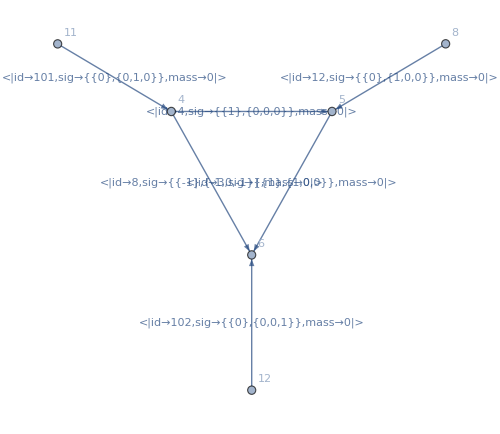

```mathematica
Cut157Right=DirectedGraph[{
DirectedEdge[4,5,4],
DirectedEdge[5,6,3],
DirectedEdge[4,6,8],
DirectedEdge[8,5,12],
DirectedEdge[11,4,101],DirectedEdge[12,6,102]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Cut157Right=DirectedGraph[AssignSignatures[Cut157Right,masses-><||>,lmb->Cut157RightLMBEdges],EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
Cut157RightcFFexpr=CrossFreeFamilyLTD[Cut157Right,ConvertToNormalisedFormat->False];
```

```mathematica
YAMLCut157Right=FormatCFFExpr[Cut157Right,Cut157RightcFFexpr];
```

```mathematica
YAMLCut157Right;
```

```mathematica
YAMLCut157Right["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"],
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[Cut157Right,DirectedGraph[cFFGetExternalEdges[Cut157Right]]]]}]
,
(#["id"])&
]
]
```

{<|mass→0,signature→{{1},{1,0,0}},id→2,power→1|>,<|mass→0,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→0,signature→{{-1},{-1,0,-1}},id→7,power→1|>}

```mathematica
YAMLCut157Right["lmb_edges"]=Block[{lmbEdges,props},
lmbEdges=Select[EdgeList[Cut157Right],MemberQ[Cut157RightLMBEdges,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"],
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,lmbEdges}]
,
(Position[Cut157RightLMBEdges,#["id"]+1]⟦1⟧⟦1⟧)&
]
]
```

{<|mass→0,signature→{{1},{0,0,0}},id→3,power→1|>}

```mathematica
cFFGetExternalEdges[Cut157Right]
```

{85<|id→12,sig→{{0},{1,0,0}},mass→0|>,114<|id→101,sig→{{0},{0,1,0}},mass→0|>,126<|id→102,sig→{{0},{0,0,1}},mass→0|>}

```mathematica
(* Reconstruct externals from orientated sums of Cutkosky cut oriented onshell momenta *)
(* Negative momenta refer to overall SG externals *)
YAMLCut157Right["external_edge_id_and_flip"]={{{-2,1}},{{7-1,1}},{{5-1,1},{1-1,-1}}};
(* Specify propagators outside of loop using oriented sum of oriented Cutkosky cut onshell momenta *)
YAMLCut157Right["non_loop_propagators"] = {{{5-1,1},{1-1,-1}}};
```

```mathematica
YAMLCut157Right["n_loop"] = 1;
```

```mathematica
YAMLCut157Right["cff_expression"]["e_surfaces"]
```

{<|edge_ids→{2,7},shift→{0,0,-1},id→0|>,<|edge_ids→{3,7},shift→{-1,0,-1},id→1|>,<|edge_ids→{2,3},shift→{-1,0,0},id→2|>,<|edge_ids→{2,7},shift→{0,0,1},id→3|>,<|edge_ids→{2,3},shift→{1,0,0},id→4|>,<|edge_ids→{3,7},shift→{1,0,1},id→5|>}

```mathematica
YAMLCut157Right;
```

```mathematica
YAMLCut157Left=<|
"edges"->{},
"lmb_edges"->{},
"external_edge_id_and_flip"->{},
"n_loop"->0,
"non_loop_propagators"->{{{5-1,1},{7-1,1}}},
"cff_expression"-><|
"e_surfaces"->{},
"terms"->{
<|
"orientation"->{},
"factors"->{
<|
"denominator"->{},
"factors"->{}
|>
}
|>
}
|>
|>
```

<|edges→{},lmb_edges→{},external_edge_id_and_flip→{},n_loop→0,non_loop_propagators→{{{4,1},{6,1}}},cff_expression→<|e_surfaces→{},terms→{<|orientation→{},factors→{<|denominator→{},factors→{}|>}|>}|>|>

```mathematica
Cut34= <|
"cut_edge_ids_and_flip"->{{1-1,-1},{5-1,1},{7-1,1}},
"left_amplitude"->YAMLCut157Left,
"right_amplitude"->YAMLCut157Right
|>;
AppendTo[YAMLSuperGraphRepr["cuts"],Cut34];
```

### Cut (#2, #5, #6)

#TODO

### Cut (#7, #8, #3)

#TODO

### Cut (#4, #8, #6)

#TODO

### Cut (#1, #5, #8, #4)

#TODO

### Cut (#2, #5, #8,#3)

#TODO

### Cut (#6, #7)

#### Left triangle of loop_induced_TriBoxTri

```mathematica
TriangleLeftLMBEdges={2};
```

```mathematica
TriangleLeft=DirectedGraph[{
DirectedEdge[1,3,2],DirectedEdge[3,7,5],
DirectedEdge[7,1,1],
DirectedEdge[103,3,7],DirectedEdge[107,7,6],DirectedEdge[101,1,11]
},VertexLabels->Automatic,EdgeLabels->Automatic];
TriangleLeft=DirectedGraph[AssignSignatures[TriangleLeft,masses-><|1->mLeft,2->mLeft,5->mLeft|>,lmb->TriangleLeftLMBEdges],EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

-Graphics-

Example evaluation:

```mathematica
NumApplication={mLeft->0.,mRight->0.,kvec->{1,3,7},lvec->{9,11,13},mvec->{15,17,19},Qvec->{0,0,0},Q0->100};
```

```mathematica
TriangleLeftNumerics={mLeft->0.,k1->{1.,2.,3.},p1->{0.,0.,0.},p2->{0.,-3.,-4.},p3->{0.,3.,4.},p1E->10.,p2E->-5.,p3E->-5.};
```

```mathematica
TriangleLeftForCLTDexpr=GeneratecLTDExpression[TriangleLeft];
```

```mathematica
EvalcLTD[TriangleLeftForCLTDexpr,TriangleLeftNumerics]//N//FullForm
```

Complex[0.,0.00651364]

```mathematica
TriangleLeftForCFFexpr=CrossFreeFamilyLTD[TriangleLeft,ConvertToNormalisedFormat->True];
```

```mathematica
TriangleLeftForCFFexpr⟦;;1⟧
```

{<|Orientation→<|2→-1,5→-1,1→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{2,1},shift_signature→{0,-1,-1}|>,<|overall_sign→1,OSE→{5,1},shift_signature→{0,0,-1}|>}|>}|>}

```mathematica
EvalcFF[TriangleLeft,TriangleLeftForCFFexpr,TriangleLeftNumerics]//N//FullForm
EvalcFF[TriangleLeft,TriangleLeftForCFFexpr⟦;;1⟧,TriangleLeftNumerics]//N//FullForm
```

Complex[0.,0.00651364]

Complex[0.,-0.0000281512]

```mathematica
TriangleLeftcFFexpr=CrossFreeFamilyLTD[TriangleLeft,ConvertToNormalisedFormat->False]
```

{{{True,True,False},1/((OSE[1]+OSE[2]) (OSE[1]+OSE[5]))},{{True,False,True},1/((OSE[1]+OSE[5]) (OSE[2]+OSE[5]))},{{True,False,False},1/((OSE[1]+OSE[2]) (OSE[2]+OSE[5]))},{{False,True,True},1/((OSE[1]+OSE[2]) (OSE[2]+OSE[5]))},{{False,True,False},1/((OSE[1]+OSE[5]) (OSE[2]+OSE[5]))},{{False,False,True},1/((OSE[1]+OSE[2]) (OSE[1]+OSE[5]))}}

```mathematica
YAMLReprTriangleLeft=FormatCFFExpr[TriangleLeft,TriangleLeftcFFexpr];
```

```mathematica
YAMLReprTriangleLeft
```

<|cff_expression→<|terms→{<|orientation→{{1,-1},{4,-1},{0,1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,-1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,1}},factors→{<|denominator→{0,3},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,1}},factors→{<|denominator→{1,5},factors→{}|>}|>,<|orientation→{{1,1},{4,1},{0,-1}},factors→{<|denominator→{4,2},factors→{}|>}|>},e_surfaces→{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}|>|>

```mathematica
YAMLReprTriangleLeft["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[TriangleLeft,DirectedGraph[cFFGetExternalEdges[TriangleLeft]]]]}]
,
(#["id"])&
]
]
```

{<|mass→0.,signature→{{1},{0,1,1}},id→0,power→1|>,<|mass→0.,signature→{{1},{0,0,0}},id→1,power→1|>,<|mass→0.,signature→{{1},{0,1,0}},id→4,power→1|>}

```mathematica
YAMLReprTriangleLeft["lmb_edges"]=Block[{lmbEdges,props},
lmbEdges=Select[EdgeList[TriangleLeft],MemberQ[TriangleLeftLMBEdges,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,lmbEdges}]
,
(Position[TriangleLeftLMBEdges,#["id"]+1]⟦1⟧⟦1⟧)&
]
]
```

{<|mass→0.,signature→{{1},{0,0,0}},id→1,power→1|>}

```mathematica
cFFGetExternalEdges[TriangleLeft]
```

{1011<|id→11,sig→{{0},{1,0,0}},mass→0|>,1033<|id→7,sig→{{0},{0,1,0}},mass→0|>,1077<|id→6,sig→{{0},{0,0,1}},mass→0|>}

```mathematica
YAMLReprTriangleLeft["external_edge_id_and_flip"]={{{-1,1}},{{7-1,-1}},{{6-1,1}}};
YAMLReprTriangleLeft["non_loop_propagators"] = {};
```

```mathematica
YAMLReprTriangleLeft["n_loop"] = 1;
```

```mathematica
YAMLReprTriangleLeft["cff_expression"]["e_surfaces"]
```

{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}

Compute some test externals

```mathematica
testLeftTriBoxTriExtValues=Block[{SGtestpoint,SGtestpointExternals,triBoxTriExt},
SGtestpoint={kvec,lvec,mvec}/.NumApplication;
SGtestpointExternals={Qvec,-Qvec}/.NumApplication;
triBoxTriExt=Table[
FullLiTriBoxTriSGEdges[extID]["sig"]⟦1⟧.SGtestpoint+FullLiTriBoxTriSGEdges[extID]["sig"]⟦2⟧.SGtestpointExternals,
{extID,{11,7,6}}
];
{
Join[{(Q0/.NumApplication)},triBoxTriExt⟦1⟧]*YAMLReprTriangleLeft["external_edge_id_and_flip"]⟦1⟧⟦2⟧,
Join[
{Sqrt[triBoxTriExt⟦2⟧.triBoxTriExt⟦2⟧+(FullLiTriBoxTriSGEdges[7]["mass"]/.NumApplication)^2]},
triBoxTriExt⟦2⟧
]*YAMLReprTriangleLeft["external_edge_id_and_flip"]⟦2⟧⟦2⟧,
Join[
(* Watchout for Cutkosoky energy sign here *)
{-Sqrt[triBoxTriExt⟦3⟧.triBoxTriExt⟦3⟧+(FullLiTriBoxTriSGEdges[6]["mass"]/.NumApplication)^2]},
triBoxTriExt⟦3⟧
]*YAMLReprTriangleLeft["external_edge_id_and_flip"]⟦3⟧⟦2⟧
}
]
```

Part::partw: Part 2 of {{-1,1}} does not exist.

Part::partw: Part 2 of {{6,-1}} does not exist.

Part::partw: Part 2 of {{5,1}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{100 {{-1,1}}⟦2⟧,0,0,0},{29.5804 {{6,-1}}⟦2⟧,15 {{6,-1}}⟦2⟧,17 {{6,-1}}⟦2⟧,19 {{6,-1}}⟦2⟧},{-29.5804 {{5,1}}⟦2⟧,15 {{5,1}}⟦2⟧,17 {{5,1}}⟦2⟧,19 {{5,1}}⟦2⟧}}

As expected since the is the triangle to the left of the Cutkosky cut with all momenta incoming, then the Qvec as positive energy but the other two from the Cutkosky cut that are also incoming into the triangle have negative energy.
Now when evaluating the energy shifts of the E-surface, defined as, Sqrt(...)+Sqrt(...)+*PLUS* Eshift, we must retain only those with positive Eshift as existing and threshold to regularise. Of course. for the real alphaLoop, all of this must be done dynamically at run time.

Now, we can specify as threshold only those with a negative energy shift

```mathematica
Table[{es,es["shift"].Table[ext⟦1⟧,{ext,testLeftTriBoxTriExtValues}]},{es,YAMLReprTriangleLeft["cff_expression"]["e_surfaces"]}]
```

Part::partw: Part 2 of {{-1.,1.}} does not exist.

Part::partw: Part 2 of {{6.,-1.}} does not exist.

Part::partw: Part 2 of {{5.,1.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,29.5804 {{5,1}}⟦2⟧-29.5804 {{6,-1}}⟦2⟧},{<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,0.+29.5804 {{5,1}}⟦2⟧},{<|edge_ids→{0,4},shift→{0,0,1},id→2|>,0.-29.5804 {{5,1}}⟦2⟧},{<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,0.-29.5804 {{6,-1}}⟦2⟧},{<|edge_ids→{0,1},shift→{0,1,1},id→4|>,-29.5804 {{5,1}}⟦2⟧+29.5804 {{6,-1}}⟦2⟧},{<|edge_ids→{1,4},shift→{0,1,0},id→5|>,0.+29.5804 {{6,-1}}⟦2⟧}}

```mathematica
(*
YAMLReprTriangleLeft["thresholds"] = Table[es["id"],{es,Select[YAMLReprTriangleLeft["cff_expression"]["e_surfaces"],((#["shift"].Table[ext⟦1⟧,{ext,testLeftTriBoxTriExtValues}])<0)&]}]
*)
```

```mathematica
YAMLReprTriangleLeft
```

<|cff_expression→<|terms→{<|orientation→{{1,-1},{4,-1},{0,1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,-1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,1}},factors→{<|denominator→{0,3},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,1}},factors→{<|denominator→{1,5},factors→{}|>}|>,<|orientation→{{1,1},{4,1},{0,-1}},factors→{<|denominator→{4,2},factors→{}|>}|>},e_surfaces→{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}|>,edges→{<|mass→0.,signature→{{1},{0,1,1}},id→0,power→1|>,<|mass→0.,signature→{{1},{0,0,0}},id→1,power→1|>,<|mass→0.,signature→{{1},{0,1,0}},id→4,power→1|>},lmb_edges→{<|mass→0.,signature→{{1},{0,0,0}},id→1,power→1|>},external_edge_id_and_flip→{{{-1,1}},{{6,-1}},{{5,1}}},non_loop_propagators→{},n_loop→1|>

```mathematica
(*MyExportYAML[YAMLReprTriangleLeft,NotebookDirectory[]<>"../data/loop_induced_TriBoxTri_left_triangle.yaml"]*)
```

#### Right triangle of loop_induced_TriBoxTri

```mathematica
TriangleRightLMBEdges={4};
```

```mathematica
TriangleRight=DirectedGraph[{
DirectedEdge[4,5,4],DirectedEdge[4,6,8],DirectedEdge[5,6,3],
DirectedEdge[3,4,7],DirectedEdge[7,6,6],DirectedEdge[8,5,12]
},VertexLabels->Automatic,EdgeLabels->Automatic];
TriangleRight=DirectedGraph[AssignSignatures[TriangleRight,masses-><|4->mRight,8->mRight,3->mRight|>,lmb->TriangleRightLMBEdges],EdgeLabels->Automatic,VertexLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

-Graphics-

Example evaluation:

```mathematica
TriangleRightNumerics={mRight->20.,k1->{4.,5.,6.},p3->{0.,0.,0.},p1->{0.,3.,4.},p2->{0.,-3.,-4.},p3E->-10.,p1E->5.,p2E->5.};
```

```mathematica
TriangleRightForCLTDexpr=GeneratecLTDExpression[TriangleRight];
```

```mathematica
EvalcLTD[TriangleRightForCLTDexpr,TriangleRightNumerics]
```

0.-4.4522×10^-8 ⅈ

```mathematica
TriangleRightForCFFexpr=CrossFreeFamilyLTD[TriangleRight,ConvertToNormalisedFormat->True];
```

```mathematica
TriangleRightForCFFexpr⟦;;1⟧
```

{<|Orientation→<|4→-1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>}

```mathematica
TriangleRightForCFFexpr
```

{<|Orientation→<|4→-1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>,<|Orientation→<|4→-1,8→-1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{4,3},shift_signature→{1,1,0}|>}|>}|>,<|Orientation→<|4→-1,8→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{8,3},shift_signature→{0,1,0}|>,<|overall_sign→1,OSE→{4,3},shift_signature→{1,1,0}|>}|>}|>,<|Orientation→<|4→1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,3},shift_signature→{-1,-1,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>,<|Orientation→<|4→1,8→1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,3},shift_signature→{-1,-1,0}|>,<|overall_sign→1,OSE→{4,8},shift_signature→{-1,0,0}|>}|>}|>,<|Orientation→<|4→1,8→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{8,3},shift_signature→{0,1,0}|>,<|overall_sign→1,OSE→{4,8},shift_signature→{-1,0,0}|>}|>}|>}

```mathematica
EvalcFF[TriangleRight,TriangleRightForCFFexpr,TriangleRightNumerics]//N//FullForm
Table[EvalcFF[TriangleRight,{cf},TriangleRightNumerics],{cf,TriangleRightForCFFexpr}]//N//FullForm
```

Complex[0.,-4.4522×10^-8]

List[Complex[0.,-7.16808×10^-9],Complex[0.,-4.99831×10^-9],Complex[0.,-4.99831×10^-9],Complex[0.,-1.00946×10^-8],Complex[0.,-1.00946×10^-8],Complex[0.,-7.16808×10^-9]]

```mathematica
[7.16807842383469428413203009814776018e-09,4.99830992408741204854054414056956505e-09,7.16807842383469428413203009814776018e-09,1.00946170067175641017834306368175397e-08,7.16807842383469428413203009814776018e-09,7.03898888672392565940294860153405232e-09]
```

```mathematica
EvalcFF[TriangleRight,{TriangleRightForCFFexpr⟦3⟧},TriangleRightNumerics]
```

0.-4.99831×10^-9 ⅈ

```mathematica
YAMLReprTriangleRight
```

<|cff_expression→<|terms→{<|orientation→{{3,-1},{7,-1},{2,-1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,-1},{2,1}},factors→{<|denominator→{2,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,1},{2,1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{3,1},{7,-1},{2,-1}},factors→{<|denominator→{4,0},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,1}},factors→{<|denominator→{3,5},factors→{}|>}|>},e_surfaces→{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}|>,edges→{<|mass→0.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→0.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→0.,signature→{{-1},{1,0,0}},id→7,power→1|>},lmb_edges→{<|mass→0.,signature→{{1},{0,0,0}},id→3,power→1|>},external_edge_id_and_flip→{{{6,1}},{{5,-1}},{{-2,1}}},non_loop_propagators→{},n_loop→1|>

```mathematica
TriangleRightcFFexpr=CrossFreeFamilyLTD[TriangleRight,ConvertToNormalisedFormat->False]
```

{{{True,True,True},1/((OSE[3]+OSE[8]) (OSE[4]+OSE[8]))},{{True,True,False},1/((OSE[3]+OSE[4]) (OSE[4]+OSE[8]))},{{True,False,False},1/((OSE[3]+OSE[4]) (OSE[3]+OSE[8]))},{{False,True,True},1/((OSE[3]+OSE[4]) (OSE[3]+OSE[8]))},{{False,False,True},1/((OSE[3]+OSE[4]) (OSE[4]+OSE[8]))},{{False,False,False},1/((OSE[3]+OSE[8]) (OSE[4]+OSE[8]))}}

```mathematica
YAMLReprTriangleRight=FormatCFFExpr[TriangleRight,TriangleRightcFFexpr];
```

```mathematica
YAMLReprTriangleRight["edges"]=Block[{props},
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,EdgeList[GraphDifference[TriangleRight,DirectedGraph[cFFGetExternalEdges[TriangleRight]]]]}]
,
(#["id"])&
]
]
```

{<|mass→0.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→0.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→0.,signature→{{-1},{1,0,0}},id→7,power→1|>}

```mathematica
YAMLReprTriangleRight["lmb_edges"]=Block[{lmbEdges,props},
lmbEdges=Select[EdgeList[TriangleRight],MemberQ[TriangleRightLMBEdges,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
SortBy[Table[
props=e/.{DirectedEdge[_,_,props_]:>props};
<|
"mass"->props["mass"]/.NumApplication,
"signature"->props["sig"],
"id"->props["id"]-1,
"power"->1
|>
,{e,lmbEdges}]
,
(Position[TriangleRightLMBEdges,#["id"]+1]⟦1⟧⟦1⟧)&
]
]
```

{<|mass→0.,signature→{{1},{0,0,0}},id→3,power→1|>}

```mathematica
cFFGetExternalEdges[TriangleRight]
```

{34<|id→7,sig→{{0},{1,0,0}},mass→0|>,76<|id→6,sig→{{0},{0,1,0}},mass→0|>,85<|id→12,sig→{{0},{0,0,1}},mass→0|>}

```mathematica
YAMLReprTriangleRight["external_edge_id_and_flip"]={{{7-1,1}},{{6-1,-1}},{{-2,1}}};
YAMLReprTriangleRight["non_loop_propagators"] = {};
```

```mathematica
YAMLReprTriangleRight["n_loop"] = 1;
```

```mathematica
YAMLReprTriangleRight["cff_expression"]["e_surfaces"]
```

{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}

Compute some test externals

```mathematica
testRightTriBoxTriExtValues=Block[{SGtestpoint,SGtestpointExternals,triBoxTriExt},
SGtestpoint={kvec,lvec,mvec}/.NumApplication;
SGtestpointExternals={Qvec,-Qvec}/.NumApplication;
triBoxTriExt=Table[
FullLiTriBoxTriSGEdges[extID]["sig"]⟦1⟧.SGtestpoint+FullLiTriBoxTriSGEdges[extID]["sig"]⟦2⟧.SGtestpointExternals,
{extID,{7,6,12}}
];
{
Join[
{Sqrt[triBoxTriExt⟦1⟧.triBoxTriExt⟦1⟧+(FullLiTriBoxTriSGEdges[7]["mass"]/.NumApplication)^2]},
triBoxTriExt⟦1⟧
]*YAMLReprTriangleRight["external_edge_id_and_flip"]⟦1⟧⟦2⟧,
Join[
(* Watchout for Cutkosoky energy sign here *)
{-Sqrt[triBoxTriExt⟦2⟧.triBoxTriExt⟦2⟧+(FullLiTriBoxTriSGEdges[6]["mass"]/.NumApplication)^2]},
triBoxTriExt⟦2⟧
]*YAMLReprTriangleRight["external_edge_id_and_flip"]⟦2⟧⟦2⟧,
(* Sign flip necessary here too *)
Join[{(-Q0/.NumApplication)},triBoxTriExt⟦1⟧]*YAMLReprTriangleRight["external_edge_id_and_flip"]⟦3⟧⟦2⟧
}
]
```

Part::partw: Part 2 of {{6,1}} does not exist.

Part::partw: Part 2 of {{5,-1}} does not exist.

Part::partw: Part 2 of {{-2,1}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{29.5804 {{6,1}}⟦2⟧,15 {{6,1}}⟦2⟧,17 {{6,1}}⟦2⟧,19 {{6,1}}⟦2⟧},{-29.5804 {{5,-1}}⟦2⟧,15 {{5,-1}}⟦2⟧,17 {{5,-1}}⟦2⟧,19 {{5,-1}}⟦2⟧},{-100 {{-2,1}}⟦2⟧,15 {{-2,1}}⟦2⟧,17 {{-2,1}}⟦2⟧,19 {{-2,1}}⟦2⟧}}

As expected since the is the triangle to the right of the Cutkosky cut with all momenta incoming, then the Qvec as positive energy but the other two from the Cutkosky cut that are also incoming into the triangle have negative energy.
Now when evaluating the energy shifts of the E-surface, defined as, Sqrt(...)+Sqrt(...)+*PLUS* Eshift, we must retain only those with positive Eshift as existing and threshold to regularise. Of course. for the real alphaLoop, all of this must be done dynamically at run time.

Now, we can specify as threshold only those with a negative energy shift

```mathematica
Table[{es,es["shift"].Table[ext⟦1⟧,{ext,testRightTriBoxTriExtValues}]},{es,YAMLReprTriangleRight["cff_expression"]["e_surfaces"]}]
```

Part::partw: Part 2 of {{6.,1.}} does not exist.

Part::partw: Part 2 of {{5.,-1.}} does not exist.

Part::partw: Part 2 of {{-2.,1.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,0.+29.5804 {{5,-1}}⟦2⟧},{<|edge_ids→{3,7},shift→{1,0,0},id→1|>,0.+29.5804 {{6,1}}⟦2⟧},{<|edge_ids→{2,3},shift→{1,1,0},id→2|>,-29.5804 {{5,-1}}⟦2⟧+29.5804 {{6,1}}⟦2⟧},{<|edge_ids→{2,7},shift→{0,1,0},id→3|>,0.-29.5804 {{5,-1}}⟦2⟧},{<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,29.5804 {{5,-1}}⟦2⟧-29.5804 {{6,1}}⟦2⟧},{<|edge_ids→{3,7},shift→{-1,0,0},id→5|>,0.-29.5804 {{6,1}}⟦2⟧}}

```mathematica
(*
YAMLReprTriangleRight["thresholds"] = Table[es["id"],{es,Select[YAMLReprTriangleRight["cff_expression"]["e_surfaces"],((#["shift"].Table[ext⟦1⟧,{ext,testRightTriBoxTriExtValues}])<0)&]}]
*)
```

```mathematica
TriangleRightcFFexpr
```

{{{True,True,True},1/((OSE[3]+OSE[8]) (OSE[4]+OSE[8]))},{{True,True,False},1/((OSE[3]+OSE[4]) (OSE[4]+OSE[8]))},{{True,False,False},1/((OSE[3]+OSE[4]) (OSE[3]+OSE[8]))},{{False,True,True},1/((OSE[3]+OSE[4]) (OSE[3]+OSE[8]))},{{False,False,True},1/((OSE[3]+OSE[4]) (OSE[4]+OSE[8]))},{{False,False,False},1/((OSE[3]+OSE[8]) (OSE[4]+OSE[8]))}}

```mathematica
CrossFreeFamilyLTD[TriangleRight,ConvertToNormalisedFormat->True]
```

{<|Orientation→<|4→-1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>,<|Orientation→<|4→-1,8→-1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,8},shift_signature→{1,0,0}|>,<|overall_sign→1,OSE→{4,3},shift_signature→{1,1,0}|>}|>}|>,<|Orientation→<|4→-1,8→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{8,3},shift_signature→{0,1,0}|>,<|overall_sign→1,OSE→{4,3},shift_signature→{1,1,0}|>}|>}|>,<|Orientation→<|4→1,8→-1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,3},shift_signature→{-1,-1,0}|>,<|overall_sign→1,OSE→{8,3},shift_signature→{0,-1,0}|>}|>}|>,<|Orientation→<|4→1,8→1,3→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{4,3},shift_signature→{-1,-1,0}|>,<|overall_sign→1,OSE→{4,8},shift_signature→{-1,0,0}|>}|>}|>,<|Orientation→<|4→1,8→1,3→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|overall_sign→1,OSE→{8,3},shift_signature→{0,1,0}|>,<|overall_sign→1,OSE→{4,8},shift_signature→{-1,0,0}|>}|>}|>}

```mathematica
YAMLReprTriangleRight
```

<|cff_expression→<|terms→{<|orientation→{{3,-1},{7,-1},{2,-1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,-1},{2,1}},factors→{<|denominator→{2,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,1},{2,1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{3,1},{7,-1},{2,-1}},factors→{<|denominator→{4,0},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,1}},factors→{<|denominator→{3,5},factors→{}|>}|>},e_surfaces→{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}|>,edges→{<|mass→0.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→0.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→0.,signature→{{-1},{1,0,0}},id→7,power→1|>},lmb_edges→{<|mass→0.,signature→{{1},{0,0,0}},id→3,power→1|>},external_edge_id_and_flip→{{{6,1}},{{5,-1}},{{-2,1}}},non_loop_propagators→{},n_loop→1|>

#### Adding the cut

```mathematica
Cut67= <|
"cut_edge_ids_and_flip"->{{6-1,-1},{7-1,1}},
"left_amplitude"->YAMLReprTriangleLeft,
"right_amplitude"->YAMLReprTriangleRight
|>
```

<|cut_edge_ids_and_flip→{{5,-1},{6,1}},left_amplitude→<|cff_expression→<|terms→{<|orientation→{{1,-1},{4,-1},{0,1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,-1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{1,-1},{4,1},{0,1}},factors→{<|denominator→{0,3},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{1,1},{4,-1},{0,1}},factors→{<|denominator→{1,5},factors→{}|>}|>,<|orientation→{{1,1},{4,1},{0,-1}},factors→{<|denominator→{4,2},factors→{}|>}|>},e_surfaces→{<|edge_ids→{0,1},shift→{0,-1,-1},id→0|>,<|edge_ids→{0,4},shift→{0,0,-1},id→1|>,<|edge_ids→{0,4},shift→{0,0,1},id→2|>,<|edge_ids→{1,4},shift→{0,-1,0},id→3|>,<|edge_ids→{0,1},shift→{0,1,1},id→4|>,<|edge_ids→{1,4},shift→{0,1,0},id→5|>}|>,edges→{<|mass→0.,signature→{{1},{0,1,1}},id→0,power→1|>,<|mass→0.,signature→{{1},{0,0,0}},id→1,power→1|>,<|mass→0.,signature→{{1},{0,1,0}},id→4,power→1|>},lmb_edges→{<|mass→0.,signature→{{1},{0,0,0}},id→1,power→1|>},external_edge_id_and_flip→{{{-1,1}},{{6,-1}},{{5,1}}},non_loop_propagators→{},n_loop→1|>,right_amplitude→<|cff_expression→<|terms→{<|orientation→{{3,-1},{7,-1},{2,-1}},factors→{<|denominator→{0,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,-1},{2,1}},factors→{<|denominator→{2,1},factors→{}|>}|>,<|orientation→{{3,-1},{7,1},{2,1}},factors→{<|denominator→{2,3},factors→{}|>}|>,<|orientation→{{3,1},{7,-1},{2,-1}},factors→{<|denominator→{4,0},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,-1}},factors→{<|denominator→{4,5},factors→{}|>}|>,<|orientation→{{3,1},{7,1},{2,1}},factors→{<|denominator→{3,5},factors→{}|>}|>},e_surfaces→{<|edge_ids→{2,7},shift→{0,-1,0},id→0|>,<|edge_ids→{3,7},shift→{1,0,0},id→1|>,<|edge_ids→{2,3},shift→{1,1,0},id→2|>,<|edge_ids→{2,7},shift→{0,1,0},id→3|>,<|edge_ids→{2,3},shift→{-1,-1,0},id→4|>,<|edge_ids→{3,7},shift→{-1,0,0},id→5|>}|>,edges→{<|mass→0.,signature→{{1},{-1,-1,0}},id→2,power→1|>,<|mass→0.,signature→{{1},{0,0,0}},id→3,power→1|>,<|mass→0.,signature→{{-1},{1,0,0}},id→7,power→1|>},lmb_edges→{<|mass→0.,signature→{{1},{0,0,0}},id→3,power→1|>},external_edge_id_and_flip→{{{6,1}},{{5,-1}},{{-2,1}}},non_loop_propagators→{},n_loop→1|>|>

```mathematica
AppendTo[YAMLSuperGraphRepr["cuts"],Cut67];
```

### Export Supergraph

```mathematica
YAMLSuperGraphRepr;
```

```mathematica
MyExportYAML[YAMLSuperGraphRepr,NotebookDirectory[]<>"../data/TriBoxTri.yaml"]
```